```mathematica
Log likelihood for 2 types, size 2 entries
```

```mathematica
twotype2ContainerLogLike=
entriesInt11 Log[1-(1-p1)^2]+
entriesInt22 Log[1-(1-p2)^2] + 
entriesInt12 Log[1-(1-p1)(1-p2)]+
(entriesTotal11-entriesInt11)Log[(1-p1)^2]+
(entriesTotal22-entriesInt22)Log[(1-p2)^2]+
(entriesTotal12-entriesInt12)Log[(1-p1)(1-p2)]
```

entriesInt11 Log[1-(1-p1)^2]+(-entriesInt11+entriesTotal11) Log[(1-p1)^2]+entriesInt12 Log[1-(1-p1) (1-p2)]+entriesInt22 Log[1-(1-p2)^2]+(-entriesInt12+entriesTotal12) Log[(1-p1) (1-p2)]+(-entriesInt22+entriesTotal22) Log[(1-p2)^2]

```mathematica
2nd derivative
```

2 derivative nd

```mathematica
-D[twotype2ContainerLogLike,{p2,2}]/.entriesInt11->entriesTotal11(1-(1-p1)^2)/.entriesInt22->entriesTotal22(1-(1-p2)^2)/. entriesInt12->entriesTotal12( 1-(1-p1)(1-p2))
```

(entriesTotal12 (1-p1)^2)/(1-(1-p1) (1-p2))-entriesTotal22 (1-(1-p2)^2) (-2/(1-(1-p2)^2)-(4 (1-p2)^2)/((1-(1-p2)^2)^2))-((-1+p1) (entriesTotal12-entriesTotal12 (1-(1-p1) (1-p2))))/((1-p1) (1-p2)^2)+(2 (entriesTotal22-entriesTotal22 (1-(1-p2)^2)))/(1-p2)^2

```mathematica
Fisher information matrix. Negative the of the 2nd derivative matrix, with interceptions set to the expected values
```

```mathematica
FIMtwotype2container=-D[twotype2ContainerLogLike,{{p1,p2},2}]/.entriesInt11->entriesTotal11(1-(1-p1)^2)/.entriesInt22->entriesTotal22(1-(1-p2)^2)/. entriesInt12->entriesTotal12( 1-(1-p1)(1-p2))
```

{{2 entriesTotal11+(2 (entriesTotal11-entriesTotal11 (1-(1-p1)^2)))/(1-p1)^2+(4 entriesTotal11 (1-p1)^2)/(1-(1-p1)^2)+(entriesTotal12 (1-p2)^2)/(1-(1-p1) (1-p2))-((entriesTotal12-entriesTotal12 (1-(1-p1) (1-p2))) (-1+p2))/((1-p1)^2 (1-p2)),entriesTotal12-(entriesTotal12-entriesTotal12 (1-(1-p1) (1-p2)))/((1-p1) (1-p2))+(entriesTotal12 (1-p1) (1-p2))/(1-(1-p1) (1-p2))-((entriesTotal12-entriesTotal12 (1-(1-p1) (1-p2))) (-1+p2))/((1-p1) (1-p2)^2)},{entriesTotal12-(entriesTotal12-entriesTotal12 (1-(1-p1) (1-p2)))/((1-p1) (1-p2))-((-1+p1) (entriesTotal12-entriesTotal12 (1-(1-p1) (1-p2))))/((1-p1)^2 (1-p2))+(entriesTotal12 (1-p1) (1-p2))/(1-(1-p1) (1-p2)),2 entriesTotal22+(entriesTotal12 (1-p1)^2)/(1-(1-p1) (1-p2))-((-1+p1) (entriesTotal12-entriesTotal12 (1-(1-p1) (1-p2))))/((1-p1) (1-p2)^2)+(2 (entriesTotal22-entriesTotal22 (1-(1-p2)^2)))/(1-p2)^2+(4 entriesTotal22 (1-p2)^2)/(1-(1-p2)^2)}}

```mathematica
Diagonal[Sqrt[Inverse[FIMtwotype2container]]]//Simplify
```

{1/2 √(-(p1 (2-3 p1+p1^2) (4 entriesTotal22 (p1 (-1+p2)-p2) (-1+p2)+entriesTotal12 (-1+p1) (-2+p2) p2))/(entriesTotal12 entriesTotal22 (-2+p1) p1 (-1+p2)^2+entriesTotal11 (-1+p1) (4 entriesTotal22 (p1 (-1+p2)-p2) (-1+p2)+entriesTotal12 (-1+p1) (-2+p2) p2))),1/2 √(-((4 entriesTotal11 (-1+p1) (p1 (-1+p2)-p2)+entriesTotal12 (-2+p1) p1 (-1+p2)) p2 (2-3 p2+p2^2))/(entriesTotal12 entriesTotal22 (-2+p1) p1 (-1+p2)^2+entriesTotal11 (-1+p1) (4 entriesTotal22 (p1 (-1+p2)-p2) (-1+p2)+entriesTotal12 (-1+p1) (-2+p2) p2)))}

```mathematica
{1/2 √(-((p1 (2-3 p1+p1^2) (4 entriesTotal22 (p1 (-1+p2)-p2) (-1+p2)+entriesTotal12 (-1+p1) (-2+p2) p2))/(entriesTotal12 entriesTotal22 (-2+p1) p1 (-1+p2)^2+entriesTotal11 (-1+p1) (4 entriesTotal22 (p1 (-1+p2)-p2) (-1+p2)+entriesTotal12 (-1+p1) (-2+p2) p2)))),1/2 √(-(((4 entriesTotal11 (-1+p1) (p1 (-1+p2)-p2)+entriesTotal12 (-2+p1) p1 (-1+p2)) p2 (2-3 p2+p2^2))/(entriesTotal12 entriesTotal22 (-2+p1) p1 (-1+p2)^2+entriesTotal11 (-1+p1) (4 entriesTotal22 (p1 (-1+p2)-p2) (-1+p2)+entriesTotal12 (-1+p1) (-2+p2) p2))))}/.entriesTotal11->N11/.entriesTotal22->N22/.entriesTotal12->N12
```

{1/2 √(-(p1 (2-3 p1+p1^2) (4 N22 (p1 (-1+p2)-p2) (-1+p2)+N12 (-1+p1) (-2+p2) p2))/(N12 N22 (-2+p1) p1 (-1+p2)^2+N11 (-1+p1) (4 N22 (p1 (-1+p2)-p2) (-1+p2)+N12 (-1+p1) (-2+p2) p2))),1/2 √(-((4 N11 (-1+p1) (p1 (-1+p2)-p2)+N12 (-2+p1) p1 (-1+p2)) p2 (2-3 p2+p2^2))/(N12 N22 (-2+p1) p1 (-1+p2)^2+N11 (-1+p1) (4 N22 (p1 (-1+p2)-p2) (-1+p2)+N12 (-1+p1) (-2+p2) p2)))}

```mathematica
D[1/2 √(-(p1 (2-3 p1+p1^2) (4 N22 (p1 (-1+p2)-p2) (-1+p2)+N12 (-1+p1) (-2+p2) p2))/(N12 N22 (-2+p1) p1 (-1+p2)^2+N11 (-1+p1) (4 N22 (p1 (-1+p2)-p2) (-1+p2)+N12 (-1+p1) (-2+p2) p2)))/.N12->prmix*Ntot/.N11->(1-prmix)*Ntot/2/.N22->(1-prmix)*Ntot/2,p1]//Simplify
```

(-p2^2 (2+p2 (-2+prmix))^2+p1 p2 (5 p2^3 (-2+prmix)^2+8 (-1+prmix)-4 p2^2 (12-8 prmix+prmix^2)+4 p2 (9-5 prmix+prmix^2))+p1^5 (8 p2^3 (-2+prmix)-2 p2^4 (-2+prmix)+p2^2 (24-16 prmix+prmix^2)-2 p2 (8-8 prmix+prmix^2)+2 (2-3 prmix+prmix^2))-2 p1^2 (2-2 prmix-2 p2^3 (28-15 prmix+prmix^2)+2 p2^2 (27-13 prmix+prmix^2)+2 p2 (-10+7 prmix+prmix^2)+p2^4 (20-16 prmix+3 prmix^2))+p1^4 (10 p2^4 (-2+prmix)+p2 (56-43 prmix-3 prmix^2)+p2^3 (72-29 prmix-3 prmix^2)-3 (4-5 prmix+prmix^2)+p2^2 (-96+47 prmix+4 prmix^2))+2 p1^3 (6-6 prmix+p2^2 (74-30 prmix-4 prmix^2)+p2^4 (20-12 prmix+prmix^2)+2 p2^3 (-32+13 prmix+prmix^2)+p2 (-36+22 prmix+6 prmix^2)))/(√2 Ntot (-1+prmix) √((p1 (2-3 p1+p1^2) (-p2 (2+p2 (-2+prmix))+p1 (-2 p2 (-2+prmix)+p2^2 (-2+prmix)+2 (-1+prmix))))/(Ntot (-1+prmix) (p2 (2+p2 (-2+prmix))+p1^2 (-2+4 p2-2 p2^2+prmix)+p1 (2+4 p2^2-2 p2 (3+prmix))))) (p2 (2+p2 (-2+prmix))+p1^2 (-2+4 p2-2 p2^2+prmix)+p1 (2+4 p2^2-2 p2 (3+prmix)))^2)

```mathematica
Limit[(p2 (2+p2 (-2+prmix))+p1^2 (-2+4 p2-2 p2^2+prmix)+p1 (2+4 p2^2-2 p2 (3+prmix)))^2,p1->0]
```

p2^2 (2+p2 (-2+prmix))^2

```mathematica
Manipulate[Plot[-p2^2 (2+p2 (-2+prmix))^2,{p2,.01,.99}],{prmix,.01,.99}]
```

```mathematica
Inverse[FIMtwotype2container]/.entriesTotal11->total/4/.entriesTotal22->total/4/.entriesTotal12->total/2//Simplify
```

{{-((-2+p1) (-1+p1) p1 ((4-3 p2) p2+p1 (2-6 p2+3 p2^2)))/((p2 (-4+3 p2)+p1^2 (3-8 p2+4 p2^2)-2 p1 (2-7 p2+4 p2^2)) total),((-2+p1) (-1+p1) p1 (-2+p2) (-1+p2) p2)/((p2 (-4+3 p2)+p1^2 (3-8 p2+4 p2^2)-2 p1 (2-7 p2+4 p2^2)) total)},{((-2+p1) (-1+p1) p1 (-2+p2) (-1+p2) p2)/((p2 (-4+3 p2)+p1^2 (3-8 p2+4 p2^2)-2 p1 (2-7 p2+4 p2^2)) total),-((-2+p2) (-1+p2) p2 (p1 (4-6 p2)+3 p1^2 (-1+p2)+2 p2))/((p2 (-4+3 p2)+p1^2 (3-8 p2+4 p2^2)-2 p1 (2-7 p2+4 p2^2)) total)}}

```mathematica
Sqrt of the FIM for some values
```

```mathematica
Sqrt[Inverse[FIMtwotype2container]/.entriesTotal11->total/.entriesTotal22->total/.entriesTotal12->20*total]/.total->5 /.p1->.4/.p2->.2
```

{{0.0987483,0.+0.0968824 ⅈ},{0.+0.0968824 ⅈ,0.118491}}

```mathematica
t=Inverse[FIMtwotype2container/.entriesTotal11->total/.entriesTotal22->total/.entriesTotal12->0]/.total->1500 /.p1->.2/.p2->.2
Sqrt[t]
```

{{0.00006,0},{0,0.00006}}

{{0.00774597,0},{0,0.00774597}}

```mathematica
Det[{{0.007745966692414833,0},{0,0.007745966692414833}}]
```

0.00006

```mathematica
t=Inverse[FIMtwotype2container/.entriesTotal11->total/.entriesTotal22->total/.entriesTotal12->0]/.total->100 /.p1->.5/.p2->.5
Sqrt[t]
```

{{0.001875,0},{0,0.001875}}

{{0.0433013,0},{0,0.0433013}}

```mathematica
The diagonal terms (ie the SE's), where the probabilities, total entries and proportion of mixed entries are set
```

```mathematica
Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]]/.p1->.1/.p2->.5/.totalentries->200/.propmix->0
```

{0.0217945,0.0433013}

```mathematica
Various plots below.
```

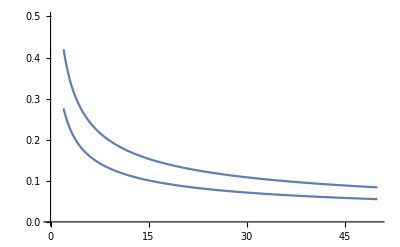

```mathematica
Plot[Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]]/.p1->.1/.p2->.5/.totalentries->tot/.propmix->.4,{tot,2,50},PlotRange->{{0,50},{0,.5}}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\cbaker1\Dropbox\Botany\CEBRA\Projects\container-line-analysis-public\asymptotic_approximation

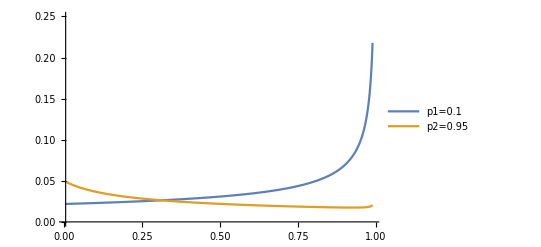
-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_095.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[1]]/.p1->.1/.p2->.95/.totalentries->200/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[2]]/.p1->.1/.p2->.95/.totalentries->200/.propmix->pr},{pr,.005,.99},PlotRange->{{0.005,.99},{0,.25}},PlotLegends->Placed[{"p1=0.1","p2=0.95"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_095.pdf",cplot]
```

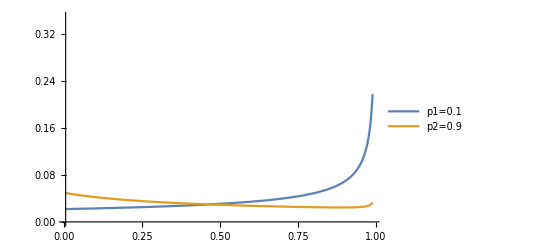
-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_09.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[1]]/.p1->.1/.p2->.9/.totalentries->200/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[2]]/.p1->.1/.p2->.9/.totalentries->200/.propmix->pr},{pr,.005,.99},PlotRange->{{0.005,.99},{0,.35}},PlotLegends->Placed[{"p1=0.1","p2=0.9"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_09.pdf",cplot]
```

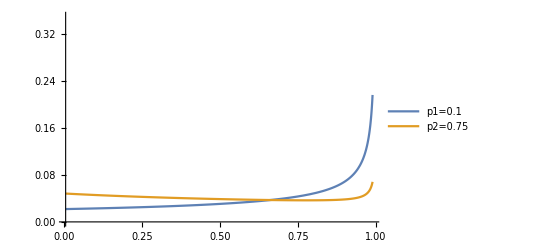
-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_075.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[1]]/.p1->.1/.p2->.75/.totalentries->200/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[2]]/.p1->.1/.p2->.75/.totalentries->200/.propmix->pr},{pr,.005,.99},PlotRange->{{0.005,.99},{0,.35}},PlotLegends->Placed[{"p1=0.1","p2=0.75"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_075.pdf",cplot]
```

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.5/.totalentries->200/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[2]]/.p1->.1/.p2->.5/.totalentries->200/.propmix->pr},{pr,.005,.99},PlotRange->{{0.005,.99},{0,.25}},PlotLegends->Placed[{"p1=0.1","p2=0.5"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_05.pdf",cplot]
```

-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_05.pdf

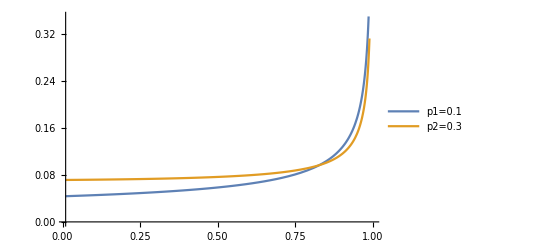
-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_03.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[1]]/.p1->.1/.p2->.3/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[2]]/.p1->.1/.p2->.3/.totalentries->50/.propmix->pr},{pr,.01,.99},PlotRange->{{.01,1},{0,.35}},PlotLegends->Placed[{"p1=0.1","p2=0.3"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_03.pdf",cplot]
```

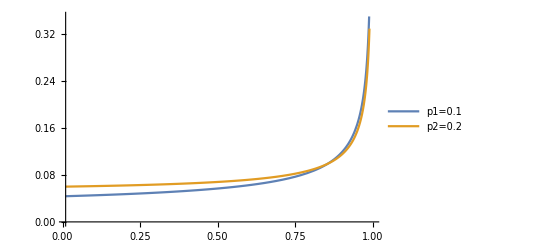
-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_02.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.2/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[2]]/.p1->.1/.p2->.2/.totalentries->50/.propmix->pr},{pr,.01,.99},PlotRange->{{.01,1},{0,.35}},PlotLegends->Placed[{"p1=0.1","p2=0.2"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_02.pdf",cplot]
```

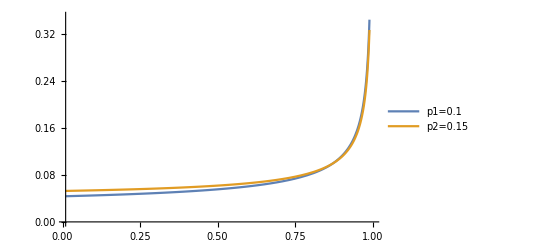
-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_015.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.15/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[2]]/.p1->.1/.p2->.15/.totalentries->50/.propmix->pr},{pr,.01,.99},PlotRange->{{.01,1},{0,.35}},PlotLegends->Placed[{"p1=0.1","p2=0.15"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_015.pdf",cplot]
```

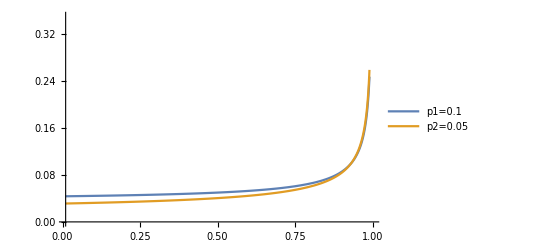
-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_005.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[1]]/.p1->.1/.p2->.05/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.singletypeentries->(totalentries-mixedentries)/2/.mixedentries->totalentries*propmix]]][[2]]/.p1->.1/.p2->.05/.totalentries->50/.propmix->pr},{pr,.01,.99},PlotRange->{{.01,1},{0,.35}},PlotLegends->Placed[{"p1=0.1","p2=0.05"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_005.pdf",cplot]
```

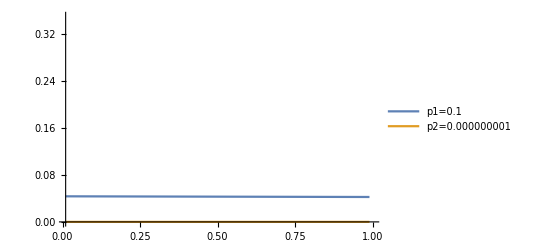
-Graphics-Standard errorProportion of mixed entries

SE_twotype_p1_01_p2_000000001.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.000000001/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[2]]/.p1->.1/.p2->.000000001/.totalentries->50/.propmix->pr},{pr,.01,.99},PlotRange->{{.01,1},{0,.35}},PlotLegends->Placed[{"p1=0.1","p2=0.000000001"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_000000001.pdf",cplot]
```

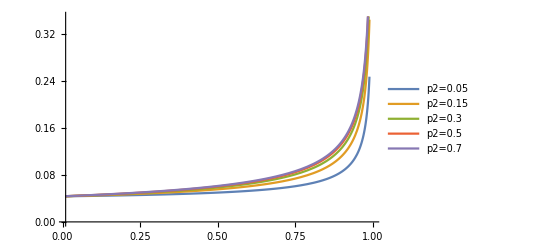
-Graphics-Standard error for p1Proportion of mixed entries

SE_twotype_p1_p2_range.pdf

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.05/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.15/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.3/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.5/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.7/.totalentries->50/.propmix->pr},{pr,.01,.99},PlotRange->{{.01,1},{0,.35}},PlotLegends->Placed[{"p2=0.05","p2=0.15","p2=0.3","p2=0.5","p2=0.7"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error for p1",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_p2_range.pdf",cplot]
```

```mathematica
cplot=Labeled[Labeled[Plot[{Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[1]]/.p1->.1/.p2->.000000001/.totalentries->50/.propmix->pr,Diagonal[Sqrt[Inverse[FIMtwotype2container/.entriesTotal11->singletypeentries/.entriesTotal22->singletypeentries/.entriesTotal12->mixedentries/.mixedentries->totalentries*propmix/.singletypeentries->(totalentries-mixedentries)/2]]][[2]]/.p1->.1/.p2->.000000001/.totalentries->50/.propmix->pr},{pr,.01,.99},PlotRange->{{.01,1},{0,.35}},PlotLegends->Placed[{"p1=0.1","p2=0.000000001"},{Left,Top}]],
Text@TraditionalForm@Style["Standard error",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Proportion of mixed entries",16]]
Export["SE_twotype_p1_01_p2_000000001.pdf",cplot]
```